# Fitting to the predicted forms

## data

```mathematica
p0s={3.85,3.825,3.80};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022}};
```

```mathematica
gp={{0.150.05,0.0900.014,0.0680.008,0.0380.008,0.0320.005,0.02110.0023,0.01630.0022,0.00850.0026,0.00590.0012,0.00540.0017,0.00450.0018,0.00380.0015,0.00240.0007,0.00200.0010,0.00180.0004,0.00190.0005,0.00130.0004},{0.1540.013,0.1750.027,0.1570.024,0.1150.026,0.0830.010,0.0680.008,0.0560.005,0.0460.009,0.0360.004,0.03030.0019,0.02480.0025,0.01960.0015,0.01500.0025,0.01060.0027,0.00670.0009,0.00420.0009},{0.1930.013,0.200.04,0.1800.022,0.1640.025,0.1390.018,0.0990.009,0.0850.009,0.0690.005,0.0580.008,0.0480.006,0.03140.0018,0.03000.0034,0.02660.0035,0.02260.0031}};(*plateau shear modulus;*)
```

```mathematica
tg={0.00007493513959359142,0.0005292353823088456,0.0021126581652639227,0.009308728608198327};
```

```mathematica
tension={{0.2422332868686113,0.12304777927124538,0.08087674266563366,0.039941897094602816,0.029826242469666343,0.01782752952655755,0.013481243374732322,0.005499136581105852,0.002223255946361173,0.0013392654052048108,0.0009871610106626824,0.0005192269692388164,0.0003246548658641914,0.00027961123994239633,0.0002039728875604251,0.0001629184313958167,0.00013270379977750913},{0.3805639982577122,0.286482996829732,0.24739465802357644,0.15379208490116492,0.10430139326631785,0.08520280674196938,0.06775324357918185,0.05342290820744475,0.0402416982891303,0.0312625093210414,0.024128023512382663,0.017941822471473915,0.011943773111877918,0.006186926696245053,0.002464072245160466,0.0007037218354227536},{0.43421294836887453,0.333905627150785,0.2917275437747871,0.25477896414719864,0.18787927807613636,0.12964357994097186,0.10586492322968272,0.08336284011725326,0.064379446869466,0.04567830183208283,0.03194401357246265,0.026861649414744428,0.022297762908372407,0.017347520231505553}};
tauAlpha={{1.1830.014,5.60.6,8.91.1,23.4.,33.4.,52.4.,70.8.,185.19.,470.41.,929.84.,1389.113.,3734.449.,7188.896.,9930.697.,2.040.1810^4,2.90.410^4,4.10.510^4},{0.7900.028,2.290.33,3.00.5,8.20.6,18.61.7,26.72.3,38.92.7,53.81.7,86.8.,117.10.,170.24.,250.27.,478.55.,1166.99.,4460.663.,1.300.2810^4},{0.8120.017,2.760.25,3.930.30,5.50.5,13.31.6,39.4.,62.9.,114.14.,225.35.,550.46.,1423.279.,2572.497.,4591.765.,8.31.210^3}};
```

```mathematica
(*perimeter contribution of bulk modulus*)
```

```mathematica
bulkModulusPeri={{3.1327868264012793,2.146669679594135,1.625445274825759,0.9613447767457817,0.7708497810237818,0.49584760259221594,0.3896030453314479,0.14924549774367601,0.045367576364034615,0.017862914323601802,0.013366041456455355,0.00727435539984978,0.008808819267151232,0.007044538150156038,0.008378659397645332,0.009381521318033909,0.004916821772182463},{3.9235712490701955,3.34492964624597,3.1090866508401844,2.394355999351477,1.81350140799965,1.5372789312579487,1.2562339007358252,1.0098889800876314,0.697893661877171,0.5144012690755295,0.31436160117244083,0.16183413459527374,0.05992257043973409,-0.1895833548666876,-0.37799115694107793,-0.2784861412942186},{3.9845466836681,3.5530111069355526,3.3680861484574054,3.092336863122748,2.56849555108396,1.7945904545591598,1.3708111421703097,0.8165136813594182,0.28331545146936116,-0.23555257510001448,-0.5267191387567112,-0.4692168330328048,-0.23833051629748753,-0.1305220947298187}};
```

## Fittings

### tension

```mathematica
tensionPrediction[kE_,kS_,p0_,p_,T_]:=1/2 kE(Log[p0/p]+Abs[Log[p0/p]]*Sqrt[1+(4kS T)/(kE( Log[p0/p])^2)]);(*Eq.12 in Matthias's paper at \gamma=0*)
```

```mathematica
tfitting=NonlinearModelFit[Flatten[Table[Table[{temperatures[[p,T]],p0s[[p]],tension[[p,T]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],1],{tensionPrediction[kE,kS,p0,p,T],{p0>3,100>kE>0,100>kS>0}},{kE,kS,p0},{T,p}]
```

FittedModel[…]

```mathematica
tfitting["BestFitParameters"]
```

{kE→22.2104,kS→0.238359,p0→3.74866}

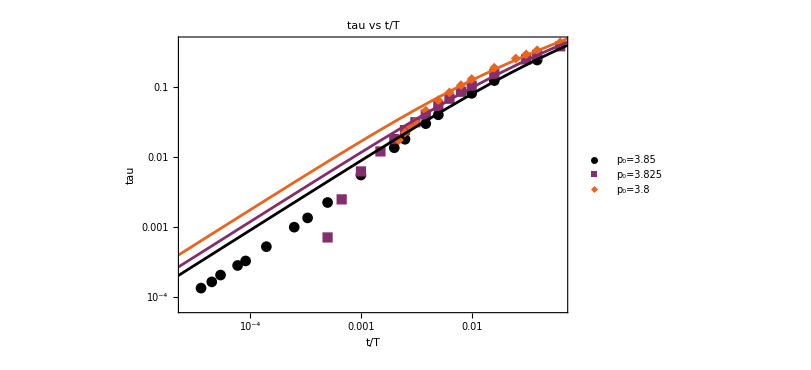

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],tension[[p,T]]},{T,Length[temperatures[[p]]]}],{p,3}],PlotStyle->gradientColScheme[5],FrameLabel->{"t/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"tau vs t/T",PlotRange->{All,All},Joined->False,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],Table[LogLogPlot[tfitting[T,p0s[[p]]],{T,0.00001,0.1},PlotStyle->gradientColScheme[5][[p]]],{p,Length[p0s]}]]
```

### shear modulus

```mathematica
gPrediction[kE_,kS_,p0_,b_,p_,T_]:=4b*1/2 kE(Log[p0/p]+Abs[Log[p0/p]]*Sqrt[1+(4kS T)/(kE( Log[p0/p])^2)]);
```

```mathematica
gfitting=NonlinearModelFit[Flatten[Table[Table[{temperatures[[p,T]],p0s[[p]],gp[[p,T]]},{T,{Length[temperatures[[p]]],Length[temperatures[[p]]],9}[[p]]}],{p,Length[p0s]}],1],{gPrediction[kE,kS,p0,b,p,T],{p0>3,100>kE>0.1,100>kS>0.1}},{kE,kS,p0,b},{T,p}]
```

FittedModel[…]

```mathematica
gfitting["BestFitParameters"]
```

{kE→40.9618,kS→1.52854,p0→3.7768,b→0.0299076}

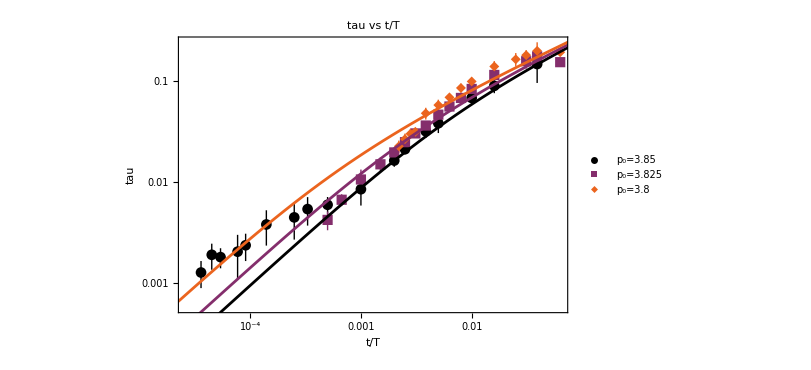

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],gp[[p,T]]},{T,Length[temperatures[[p]]]}],{p,3}],PlotStyle->gradientColScheme[5],FrameLabel->{"t/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"tau vs t/T",PlotRange->{All,All},Joined->False,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],Table[LogLogPlot[gfitting[T,p0s[[p]]],{T,0.00001,0.1},PlotStyle->gradientColScheme[5][[p]]],{p,Length[p0s]}]]
```

#### bulk modulus

```mathematica
kfitting=NonlinearModelFit[Flatten[Table[Table[{temperatures[[p,T]],p0s[[p]],bulkmodulusPeri[[p,T]]},{T,{Length[temperatures[[p]]],Length[temperatures[[p]]],9}[[p]]}],{p,Length[p0s]}],1],{gPrediction[kE,kS,p0,b,p,T],{p0>3,100>kE>1,100>kS>0.1}},{kE,kS,p0,b},{T,p}]
```

FittedModel[…]

```mathematica
kfitting["BestFitParameters"]
```

{kE→5.04177,kS→2.3914,p0→3.67328,b→1.42353}

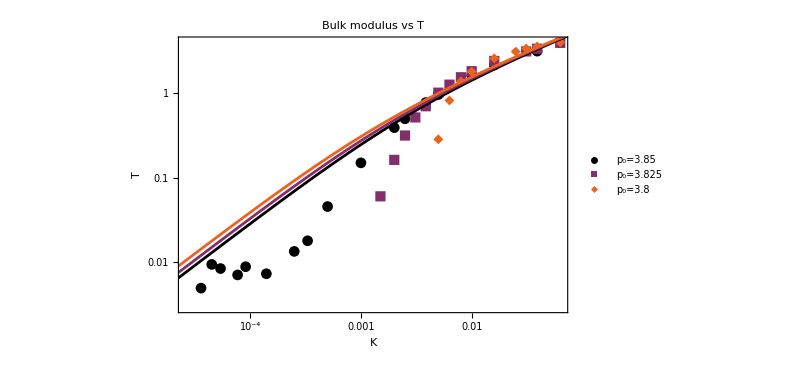

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],bulkmodulusPeri[[p,T]]},{T,Length[temperatures[[p]]]}],{p,3}],PlotStyle->gradientColScheme[5],FrameLabel->{"K ","T"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"Bulk modulus vs T",PlotRange->{All,All},Joined->False,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],Table[LogLogPlot[kfitting[T,p0s[[p]]],{T,0.00001,0.1},PlotStyle->gradientColScheme[5][[p]]],{p,Length[p0s]}]]
```

## Collapse

```mathematica
Mod[3,3]
```

0

```mathematica
Table[RGBColor[0,0,1,1-0.2*Mod[i,4]],{i,{1,2,3,1,2,3,1,2,3,1,2,3}-1}]
```

{RGBColor[0, 0, 1, 1.],RGBColor[0, 0, 1, 0.8],RGBColor[0, 0, 1, 0.6],RGBColor[0, 0, 1, 1.],RGBColor[0, 0, 1, 0.8],RGBColor[0, 0, 1, 0.6],RGBColor[0, 0, 1, 1.],RGBColor[0, 0, 1, 0.8],RGBColor[0, 0, 1, 0.6],RGBColor[0, 0, 1, 1.],RGBColor[0, 0, 1, 0.8],RGBColor[0, 0, 1, 0.6]}

```mathematica
markersClose=pm1[4,Table[RGBColor[0,0,1,1-0.4*Mod[i,4]],{i,{1,2,3,1,2,3,1,2,3,1,2,3}-1}]];
```

```mathematica
markersOpen=pm2[4,Table[RGBColor[0,0,1,1-0.3*Mod[i,4]],{i,{1,2,3,1,2,3,1,2,3,1,2,3}}]];
```

```mathematica
tfitting=NonlinearModelFit[Flatten[Table[Table[{temperatures[[p,T]],p0s[[p]],tension[[p,T]]},{T,{1,2,2}[[p]],{17,14,10}[[p]]}],{p,Length[p0s]}],1],{tensionPrediction[kE,kS,p0,p,T],{p0>3,100>kE>0,100>kS>0}},{kE,kS,p0},{T,p}]
```

FittedModel[…]

```mathematica
gpfitting=NonlinearModelFit[Flatten[Table[Table[{temperatures[[p,T]],p0s[[p]],gp[[p,T,1]]},{T,{1,2,2}[[p]],{9,16,14}[[p]]}],{p,Length[p0s]}],1],{tensionPrediction[kE,kS,p0,p,T],{p0>3,100>kE>0,100>kS>0}},{kE,kS,p0},{T,p}]
```

FittedModel[…]

```mathematica
kfitting=NonlinearModelFit[Flatten[Table[Table[{temperatures[[p,T]],p0s[[p]],bulkModulusPeri[[p,T]]},{T,1,{10,9,7}[[p]]}],{p,1,1}],1],{tensionPrediction[kE,kS,p0,p,T],{3.8>p0>3,100>kE>0,10>kS>0}},{kE,kS,p0},{T,p}]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel[…]

```mathematica
tfitting["BestFitParameters"]
```

{kE→25.3636,kS→0.231022,p0→3.75016}

```mathematica
gpfitting["BestFitParameters"]
```

{kE→7.98945,kS→0.169304,p0→3.77419}

```mathematica
kfitting["BestFitParameters"]
```

{kE→46.9508,kS→7.7749,p0→3.76546}

```mathematica
{kE->0.06906709483735421,kS->1688.0034262563995,p0->1.1455190849708623*^8}
```

{kE→0.0690671,kS→1688.,p0→1.14552×10^8}

```mathematica
openHexagon=Graphics[{EdgeForm[{Blue,Thickness[0.03]}],FaceForm[None],Polygon[Table[{Cos[θ],Sin[θ]},{θ,0,2 π,π/3}]]},PlotRange->{{-1,1},{-1,1}},AspectRatio->1,Background->Transparent,ImageSize->20]
```

-Graphics-

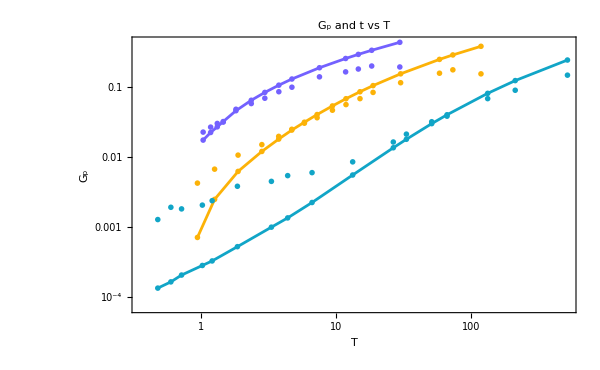

```mathematica
comparisionTensionPlot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]]/tg[[p]],tension[[p,T]]},{T,{17,16,14}[[p]]}],{p,3}],PlotMarkers->pm2[4,discreteColScheme],PlotStyle->discreteColScheme,FrameLabel->{"T ","G_p"},ImageSize->600,PlotLabel->"G_p and t vs T",PlotRange->{All,All},Joined->True,PlotLegends->Table["t p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],ListLogLogPlot[Table[Table[{temperatures[[p,T]]/tg[[p]],gp[[p,T,1]]},{T,{17,16,14}[[p]]}],{p,3}],PlotMarkers->pm1[4,discreteColScheme],FrameLabel->{"t/T ","tau"},ImageSize->600,PlotStyle->discreteColScheme,PlotLabel->"tau vs t/T",PlotRange->{All,All},PlotLegends->Table["G_p p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],Joined->False]]
```

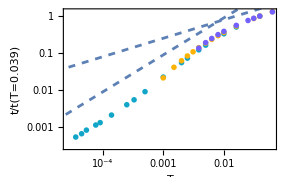

```mathematica
tensionInset=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],tension[[p,T]]/tension[[p,{1,2,2}[[p]]]]},{T,{17,14,10}[[p]]}],{p,3}],PlotMarkers->pm2[4,discreteColScheme],PlotStyle->discreteColScheme,FrameLabel->{"T ","t/t(T=0.039)"},ImageSize->4*72,PlotRange->{All,All}],LogLogPlot[90x,{x,0.00001,0.1},PlotStyle->Dashed],LogLogPlot[8x^0.5,{x,0.00001,0.1},PlotStyle->Dashed]]
```

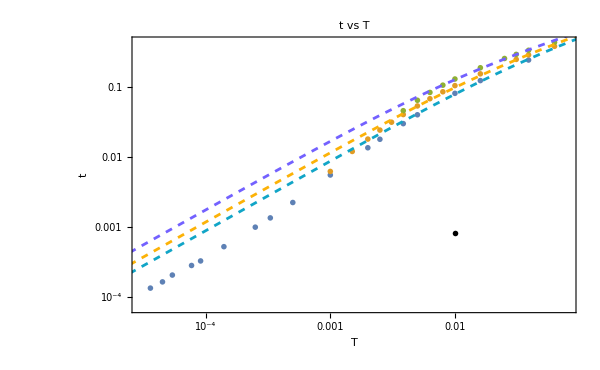

```mathematica
tTPlot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],tension[[p,T]]},{T,{17,14,10}[[p]]}],{p,3}],PlotMarkers->pm2[6,discreteColScheme],FrameLabel->{"T ","t"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"t vs T",PlotRange->{{0.00003,0.08},All},Epilog->{Inset[tensionInset,{-4.6,-7.1},Automatic]},Joined->False,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],Table[LogLogPlot[tfitting[T,p0s[[p]]],{T,0.00001,0.1},PlotStyle->{discreteColScheme[[p]],Dashed}],{p,Length[p0s]}]]
```

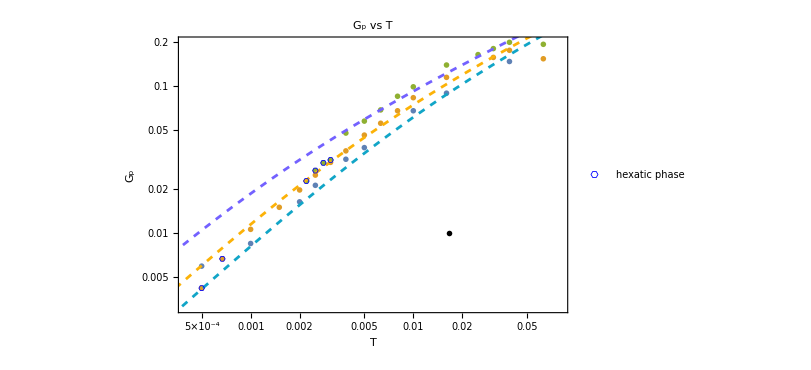

```mathematica
GpTPlot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],gp[[p,T,1]]},{T,{9,16,14}[[p]]}],{p,3}],PlotMarkers->pm1[4,discreteColScheme],FrameLabel->{"T ","G_p"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"G_p vs T",PlotRange->{{0.0004,0.08},All},Epilog->{Inset[gpInset,{-4.1,-4.6},Automatic]},Joined->False,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],Table[LogLogPlot[gpfitting[T,p0s[[p]]],{T,0.00001,0.1},PlotStyle->{discreteColScheme[[p]],Dashed}],{p,Length[p0s]}],ListLogLogPlot[Table[Table[{temperatures[[p,T]],gp[[p,T,1]]},{T,Length[temperatures[[p]]]-{8,1,3}[[p]],Length[temperatures[[p]]]}],{p,2,3}],FrameLabel->{"G_p/T ","tau"},ImageSize->600,PlotMarkers->{openHexagon,0.07},PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"G_p vs T",PlotLegends->{"hexatic phase"},PlotRange->{{2,14},All},Joined->False]]
```

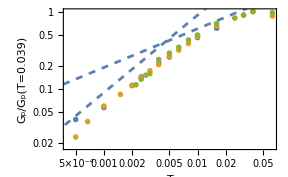

```mathematica
gpInset=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],gp[[p,T,1]]/gp[[p,{1,2,2}[[p]],1]]},{T,{9,16,14}[[p]]}],{p,3}],PlotMarkers->pm1[3,discreteColScheme],ImageSize->4*72.,PlotRange->{All,All},Joined->False,FrameLabel->{"T ","G_p/G_p(T=0.039)"}],LogLogPlot[90x,{x,0.00001,0.1},PlotStyle->Dashed],LogLogPlot[6x^0.5,{x,0.00001,0.1},PlotStyle->Dashed]]
```

```mathematica
bulkmodulusPeri
```

{{3.13279,2.14667,1.62545,0.961345,0.77085,0.495848,0.389603,0.149245,0.0453676,0.0178629,0.013366,0.00727436,0.00880882,0.00704454,0.00837866,0.00938152,0.00491682},{3.92357,3.34493,3.10909,2.39436,1.8135,1.53728,1.25623,1.00989,0.697894,0.514401,0.314362,0.161834,0.0599226,-0.189583,-0.377991,-0.278486},{3.98455,3.55301,3.36809,3.09234,2.5685,1.79459,1.37081,0.816514,0.283315,-0.235553,-0.526719,-0.469217,-0.238331,-0.130522}}

```mathematica
bulkModulusPeri
```

{{3.98455,3.55301,3.36809,3.09234,2.5685,1.79459,1.37081,0.816514,0.283315,-0.235553,-0.526719,-0.469217,-0.238331,-0.130522},{3.92357,3.34493,3.10909,2.39436,1.8135,1.53728,1.25623,1.00989,0.697894,0.514401,0.314362,0.161834,0.0599226,-0.189583,-0.377991,-0.278486},{3.13279,2.14667,1.62545,0.961345,0.77085,0.495848,0.389603,0.149245,0.0453676,0.0178629,0.013366,0.00727436,0.00880882,0.00704454,0.00837866,0.00938152,0.00491682}}

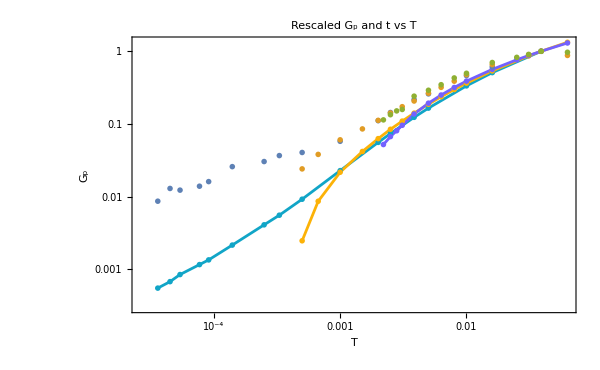

```mathematica
comparisionTensionPlot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],tension[[p,T]]/tension[[p,{1,2,2}[[p]]]]},{T,{17,16,14}[[p]]}],{p,3}],PlotMarkers->pm2[4,discreteColScheme],FrameLabel->{"T","G_p"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"Rescaled G_p and t vs T",PlotRange->{All,All},Joined->True,PlotStyle->discreteColScheme,PlotStyle->Dashed,PlotLegends->Table["t p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],ListLogLogPlot[Table[Table[{temperatures[[p,T]],gp[[p,T,1]]/gp[[p,{1,2,2}[[p]],1]]},{T,Length[temperatures[[p]]]}],{p,3}],PlotMarkers->pm1[4,discreteColScheme],FrameLabel->{"t/T ","tau"},ImageSize->600,PlotLabel->"tau vs t/T",PlotRange->{All,All},Joined->False,PlotLegends->Table["G_p p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]]]
```

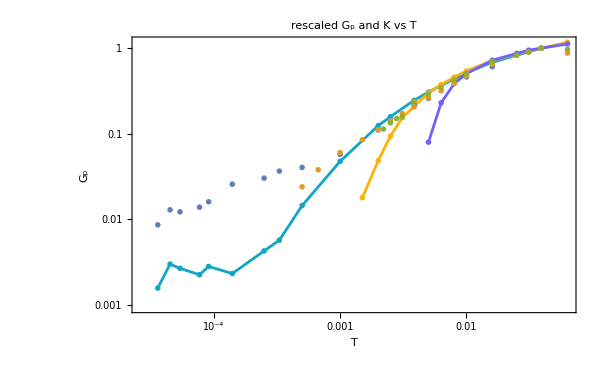

```mathematica
comparisionBulkPlot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],bulkModulusPeri[[p,T]]/bulkModulusPeri[[p,{1,2,2}[[p]]]]},{T,{17,16,14}[[p]]}],{p,3}],PlotMarkers->pm2[4,discreteColScheme],FrameLabel->{"T","G_p"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"rescaled G_p and K vs T",PlotRange->{All,All},Joined->True,PlotStyle->discreteColScheme,PlotStyle->Dashed,PlotLegends->Table["K p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],ListLogLogPlot[Table[Table[{temperatures[[p,T]],gp[[p,T,1]]/gp[[p,{1,2,2}[[p]],1]]},{T,Length[temperatures[[p]]]}],{p,3}],PlotMarkers->pm1[4,discreteColScheme],FrameLabel->{"t/T ","tau"},ImageSize->600,PlotLabel->"tau vs t/T",PlotRange->{All,All},Joined->False,PlotLegends->Table["G_p p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]]]
```

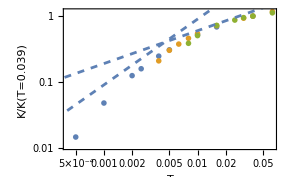

```mathematica
KInset=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],bulkModulusPeri[[p,T]]/bulkModulusPeri[[p,{1,2,2}[[p]]]]},{T,{9,9,7}[[p]]}],{p,3}],PlotMarkers->pm1[3,discreteColScheme],ImageSize->4*72.,PlotRange->{All,All},Joined->False,FrameLabel->{"T ","K/K(T=0.039)"}],LogLogPlot[90x,{x,0.00001,0.1},PlotStyle->Dashed],LogLogPlot[6x^0.5,{x,0.00001,0.1},PlotStyle->Dashed]]
```

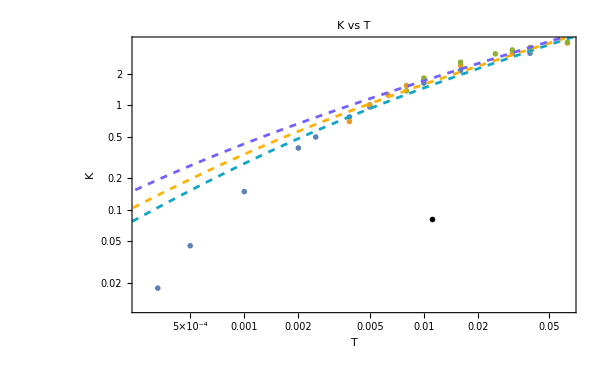

```mathematica
KTPlot=Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],bulkModulusPeri[[p,T]]},{T,{10,9,7}[[p]]}],{p,3}],PlotMarkers->pm2[4,discreteColScheme],FrameLabel->{"T ","K"},Epilog->{Inset[KInset,{-4.5,-2.5},Automatic]},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"K vs T",PlotRange->{All,All},Joined->False,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],Table[LogLogPlot[kfitting[T,p0s[[p]]],{T,0.00001,0.1},PlotStyle->{discreteColScheme[[p]],Dashed}],{p,Length[p0s]}]]
```

```mathematica
Export["/home/chengling/Research/updates/08152024/fitting.jpeg",Grid[Partition[{GpTPlot,tTPlot,KTPlot},1]],ImageResolution->400]
```

/home/chengling/Research/updates/08152024/fitting.jpeg

```mathematica
Export["/home/chengling/Research/updates/08152024/compare.jpeg",Grid[Partition[{comparisionTensionPlot,comparisionBulkPlot},1]],ImageResolution->400]
```

/home/chengling/Research/updates/08152024/compare.jpeg